## Underdominance

### Writing the equations

Set of eqs

```mathematica
dnaa=m[NN]NN (paa^2*1 +2paa pAa *1/2+2paa pAA *0+pAa^2*1/4+2pAa pAA*0+pAA^2*0)ωaa -d[NN]NN paa;
dnAa=m[NN]NN (paa^2*0 +2paa pAa *1/2+2paa pAA *1+pAa^2*1/2+2pAa pAA*1/2+pAA^2*0)ωAa -d[NN]NN pAa;
dnAA=m[NN]NN (paa^2*0 +2paa pAa *0+2paa pAA *0+pAa^2*1/4+2pAa pAA*1/2+pAA^2*1)ωAA -d[NN]NN pAA;
```

```mathematica
Solve[ωb==paa ωaa+pAa ωAa+(1-paa-pAa) ωAA,ωAA]//Simplify
```

{{ωAA→(paa ωaa+pAa ωAa-ωb)/(-1+paa+pAa)}}

Total density of the population

```mathematica
dNN=dnaa+dnAa+dnAA/.pAA->1-paa-pAa//FullSimplify
```

-NN d[NN]+1/4 NN (4 ωAA+(2 paa+pAa) (4 (ωAa-ωAA)+(2 paa+pAa) (ωaa-2 ωAa+ωAA))) m[NN]

Rewrite the equations in terms of genotype frequencies

```mathematica
dpaa=1/NN dnaa-1/NN dNN paa//FullSimplify
dpAa=1/NN dnAa-1/NN dNN pAa//FullSimplify
dpAA=1/NN dnAA-1/NN dNN pAA//FullSimplify
```

-1/4 ((2 paa+pAa) ((-1+paa) (2 paa+pAa) ωaa-2 paa (-2+2 paa+pAa) ωAa)+paa (-2+2 paa+pAa)^2 ωAA) m[NN]

-1/4 ((2 paa+pAa) (pAa (2 paa+pAa) ωaa-2 (pAa (-1+2 paa+pAa)+2 pAA) ωAa)+pAa (-2+2 paa+pAa)^2 ωAA) m[NN]

-1/4 ((2 paa+pAa) pAA ((2 paa+pAa) (ωaa-2 ωAa)+4 ωAa)+(pAa^2 (-1+pAA)+4 (-2+paa) pAa pAA+4 ((-1+paa)^2-pAA) pAA) ωAA) m[NN]

Small consistency check

```mathematica
dpaa+dpAa+dpAA/.{pAA->1-paa-pAa}//FullSimplify
```

0

Rewrite the variables; find set of replacement rules to go from the original to the new variables

```mathematica
Solve[{NN==nAA+nAa+naa,pa== naa/NN+1/2 nAa/NN,dHW== nAa/NN-2(naa/NN+1/2 nAa/NN)(nAA/NN+1/2 nAa/NN)},{nAA,nAa,naa}]
newvars=%⟦1⟧;
```

{{nAA→-1/2 NN (-2+dHW+4 pa-2 pa^2),nAa→NN (dHW+2 pa-2 pa^2),naa→1/2 (-dHW NN+2 NN pa^2)}}

Intermediate replacement rules (from genotype freqs to densities)

```mathematica
npvars={paa-> naa/NN,pAa-> nAa/NN,pAA-> nAA/NN};
```

Rewrite change in total population density with the new variables

```mathematica
dNNs=dNN/.npvars/.newvars//FullSimplify
```

NN (-d[NN]+(2 pa (ωAa-ωAA)+ωAA+pa^2 (ωaa-2 ωAa+ωAA)) m[NN])

-> Note that dNNs only depends on NN and pa, but not on dHW, the deviation from Hardy-Weinberg frequencies

Changes in allele frequencies

```mathematica
dpas=dpa=dpaa+1/2 dpAa/.npvars/.newvars//FullSimplify
```

-(-1+pa) pa (ωAa-ωAA+pa (ωaa-2 ωAa+ωAA)) m[NN]

```mathematica
dpA=dpAA+1/2 dpAa/.npvars/.newvars//FullSimplify
```

(-1+pa) pa (ωAa-ωAA+pa (ωaa-2 ωAa+ωAA)) m[NN]

Small consistency check

```mathematica
dpa+dpA//FullSimplify
```

0

Deviation from Hardy-Weinberg
First write the derivative

```mathematica
D[pAa[t]-2(pa[t])(1-pa[t]),t]//FullSimplify
```

(-2+4 pa[t]) pa'[t]+pAa'[t]

```mathematica
ddHW=dpAa-dpa(4pa-2)/.npvars/.newvars//FullSimplify
```

(-2 (-2+dHW) pa (ωAa-ωAA)-dHW ωAA+6 pa^4 (ωaa-2 ωAa+ωAA)-8 pa^3 (ωaa-3 ωAa+2 ωAA)-pa^2 ((-2+dHW) ωaa-2 (-8+dHW) ωAa+(-14+dHW) ωAA)) m[NN]

Derivation from HW exists even when is =0 at the initial time:

```mathematica
ddHW/.dHW->0//FullSimplify
```

2 (-1+pa) pa (-2 ωAa+2 ωAA+3 pa^2 (ωaa-2 ωAa+ωAA)-pa (ωaa-6 ωAa+5 ωAA)) m[NN]

just decays when no selection

```mathematica
ddHW/.{ωaa->1,ωAa->1,ωAA->1}//FullSimplify
```

-dHW m[NN]

Conclusion

```mathematica
dNNs
dpas
```

NN (-d[NN]+(2 pa (ωAa-ωAA)+ωAA+pa^2 (ωaa-2 ωAa+ωAA)) m[NN])

-(-1+pa) pa (ωAa-ωAA+pa (ωaa-2 ωAa+ωAA)) m[NN]

### Quick analysis

#### Define demographic functions

```mathematica
demog1={d[NN]->d NN, m[NN]->b};
demog2={d[NN]->d , m[NN]->b(1-NN/KK)};
demog3={d[NN]->d1+ NN d2 , m[NN]->b};
```

Viability

```mathematica
dNA=dNNs/.pa->1//FullSimplify
```

-NN d[NN]+NN ωaa m[NN]

Stability of pop extinction equilibrium

```mathematica
(D[dNA,NN])/.NN->0
```

-d[0]+ωaa m[0]

```mathematica
(D[dNA/.demog1,NN])/.NN->0
(D[dNA/.demog2,NN])/.NN->0
```

b ωaa

-d+b ωaa

```mathematica
(D[dNA/.demog3,NN])/.NN->0
```

-d1+b ωaa

```mathematica
Solve[(dNA/.demog1)==0,NN]
```

{{NN→0},{NN→(b ωaa)/d}}

```mathematica
Solve[(dNA/.demog2)==0,NN]
```

{{NN→0},{NN→(KK (-d+b ωaa))/(b ωaa)}}

```mathematica
Solve[(dNA/.demog3)==0,NN]
```

{{NN→0},{NN→(-d1+b ωaa)/d2}}

So cannot use demog1 if we want to be able to consider population extinction

#### Analysis

```mathematica
Solve[dpas==0,pa]//FullSimplify
soleq=%⟦3⟧;
```

{{pa→0},{pa→1},{pa→(-ωAa+ωAA)/(ωaa-2 ωAa+ωAA)}}

```mathematica
AF[x_]:=Assuming[ωAA≥0&&ωAA≤1&&ωAa≥0&&ωAa≤1&&ωaa≥0&&ωaa≤1&&m[NN]≥0&&d[NN]≥0, FullSimplify[x]]
```

```mathematica
condsAdm=Reduce[(pa/.soleq)≤ 1 && (pa/.soleq)≥ 0]//AF
```

(ωAa<ωAA&&ωaa≥ωAa)||(ωAa==ωAA&&ωaa≠ωAa)||(ωAa>ωAA&&ωaa≤ωAa)

The intermediate solution is admissible if we either have under- or over-dominance.

Stability of the intermediate solution

```mathematica
Ddpae=(D[dpas,pa])/.soleq//AF
```

-((ωaa-ωAa) (ωAa-ωAA) m[NN])/(ωaa-2 ωAa+ωAA)

```mathematica
Reduce[(Ddpae<0)&&condsAdm]//AF
```

ωAa>ωAA&&ωaa<ωAa&&m[NN]>0

The intermediate solution is admissible and locally stable only in the case of overdominance.

```mathematica
Reduce[(Ddpae>0)&&condsAdm]//AF
```

ωAa<ωAA&&ωaa>ωAa&&m[NN]>0

and we have a bistability in the case of underdominance

```mathematica
soleq/.{ωAA->ωaa}//FullSimplify
```

{pa→1/2}

```mathematica
Reduce[(pa/.soleq)>1/2&&ωAa<ωAA&&ωaa>ωAa]//AF
```

ωAa<ωaa<ωAA

## Cytoplasmic incompatibility

### Equations

wF, wM, sF, sM

```mathematica
dwF=.;dwM=.;
```

```mathematica
dwF=1/2(wF/NN wM/NN fw+wF/NN sM/NN fw)b[NN]NN-δwF wF;
dwM=1/2(wF/NN wM/NN fw+wF/NN sM/NN fw)b[NN]NN -δwM wM;
dsF=1/2(sF/NN wM/NN fs ωH+sF/NN sM/NN fs)b[NN]NN -δwF wF;
dsM=1/2(sF/NN wM/NN fs ωH+sF/NN sM/NN fs)b[NN]NN -δwM wM;
```

```mathematica
dwF+dwM//Simplify
```

-wF δwF-wM δwM+(fw wF (sM+wM) b[NN])/NN

```mathematica
dsF+dsM//Simplify
```

-wF δwF-wM δwM+(fs sF (sM+wM ωH) b[NN])/NN

```mathematica
dnw=((nw/NN)^2 fw+nw/NN ns/NN fw)b[NN]NN-d[NN]nw;
dns=(ns/NN nw/NN ωH+(ns/NN)^2)b[NN]NN -d[NN]ns;
```

```mathematica
Solve[{NN==ns+nw,p== nw/(ns+nw)},{ns,nw}]
chgvar=%⟦1⟧;
```

{{ns→NN-NN p,nw→NN p}}

```mathematica
dNN=dnw+dns/.chgvar//FullSimplify
Collect[%,p,FullSimplify]
```

NN (b[NN]+p (-2+fw+p+ωH-p ωH) b[NN]-d[NN])

-NN p^2 (-1+ωH) b[NN]+NN p (-2+fw+ωH) b[NN]+NN (b[NN]-d[NN])

```mathematica
dp=1/NN dnw-1/NN dNN p/.chgvar//FullSimplify
```

-(-1+p) p (-1+fw+p-p ωH) b[NN]

Find interior equilibrium and check admissibility

```mathematica
Solve[dp==0,p]
soleq=%⟦3⟧;
```

{{p→0},{p→1},{p→(-1+fw)/(-1+ωH)}}

```mathematica
AF[x_]:=Assuming[ωH≥0&&ωH≤1&&fw≥0&&fw≤1&&b[NN]≥0&&d[NN]≥0,FullSimplify[x]]
```

```mathematica
condsAdm=Reduce[(p/.soleq)≥0&&(p/.soleq)≤1]//AF
```

ωH<1&&ωH≤fw

Stability of the interior equilibrium

```mathematica
ddpeq=(D[dp,p])/.soleq//FullSimplify
```

((-1+fw) (fw-ωH) b[NN])/(-1+ωH)

```mathematica
Reduce[ddpeq> 0&&condsAdm]//AF
```

ωH<fw<1&&b[NN]>0

```mathematica
dNN/.p->1//FullSimplify
dNN/.p->0//FullSimplify
```

NN (fw b[NN]-d[NN])

NN (b[NN]-d[NN])

```mathematica
Reduce[(p/.soleq)< 1/2&&condsAdm]//AF
```

1+ωH<2 fw

Stability conditions for total population size

```mathematica
dNN0=dNN/.p->0
```

NN (b[NN]-d[NN])

```mathematica
dNN1=dNN/.p->1//FullSimplify
```

NN (fw b[NN]-d[NN])

```mathematica
dNN
```

NN (b[NN]+p (-2+fw+p+ωH-p ωH) b[NN]-d[NN])

```mathematica
dp
```

-(-1+p) p (-1+fw+p-p ωH) b[NN]

```mathematica
demogt={b[NN[t]]->r(1-NN[t]/KK)+1, d[NN[t]]->1};
dNNt=NN[t] (b[NN[t]]+p[t] (-2+fw+p[t]+ωH-p[t] ωH) b[NN[t]]-d[NN[t]])/.demogt
dpt=-(-1+p[t]) p[t] (-1+fw+p[t]-p[t] ωH) b[NN[t]]/.demogt
```

NN[t] (r (1-NN[t]/KK)+(1+r (1-NN[t]/KK)) p[t] (-2+fw+ωH+p[t]-ωH p[t]))

(1+r (1-NN[t]/KK)) (1-p[t]) p[t] (-1+fw+p[t]-ωH p[t])

```mathematica
pstar=(1-fw)/(1-ωH);
```

```mathematica
Assuming[fw>0&&fw<1&&ωH>0&&ωH<1&&ωH≤fw, Simplify[Reduce[pstar<1/2, ωH]]]
```

1+ωH<2 fw

{{NN→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

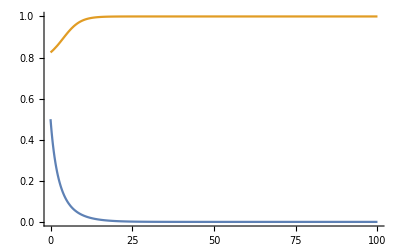

```mathematica
parms={r->1,fw->0.4,ωH->0.2, KK->1000};
inits={N0->500, p0->1.1*pstar/.parms};
tf=100;
sol=NDSolve[{NN'[t]==dNNt/.parms,p'[t]==dpt/.parms,NN[0]==N0/.inits,p[0]==p0/.inits},{NN,p},{t,0,tf}]
Plot[{Evaluate[NN[t]/KK/.parms/.sol],Evaluate[p[t]/.sol]},{t,0,tf},PlotRange->All]
```